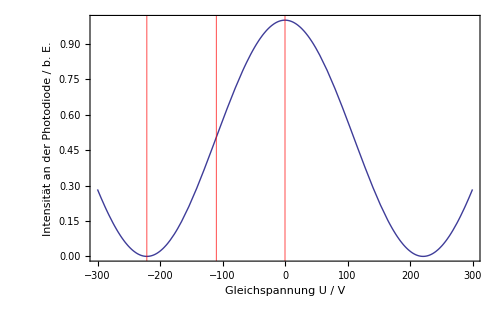

```mathematica
Ι=Cos[π U/(2*221)]^2;
Plot[Ι,{U,-300,300},ImageSize->500,Frame->True,LabelStyle->Directive[FontSize->14],FrameLabel->{"Gleichspannung U / V","Intensität an der Photodiode / b. E."},GridLines->{{0,-110,-221},{}},GridLinesStyle->Red,Axes->False]
```

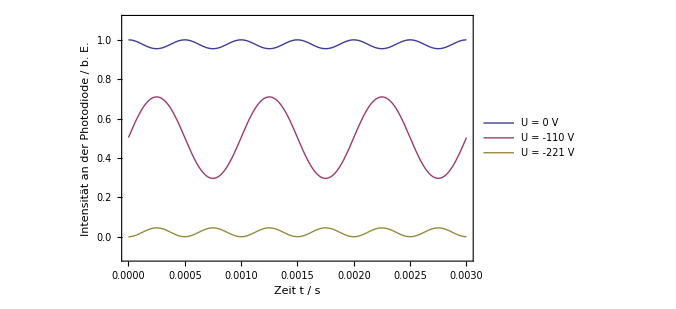

```mathematica
l1={U->U0+A Sin[2π*1000*t]};
l2a={U0->0,A->30};
l2b={U0->-110,A->30};
l2c={U0->-221,A->30};
Plot[{Ι/.l1/.l2a,Ι/.l1/.l2b,Ι/.l1/.l2c},{t,0,0.003},PlotRange->{-0.1,1.1},Frame->True,ImageSize->500,FrameLabel->{"Zeit t / s","Intensität an der Photodiode / b. E."},LabelStyle->Directive[FontSize->14],PlotLegends->{"U =    0 V","U = -110 V","U = -221 V"}]
```

```mathematica
p3=Plot3D[Sin[π(U0+A Sin[2 π *1000*t])/(2*221)]^2/.A->30,{U0,-300,300},{t,0,0.003},ImageSize->600,AxesLabel->{"Gleichspannung / V","Zeit t / s","Intensität an der \n Photodiode / b. E."},MeshFunctions->{#1&,#1&},Mesh->{{-221,-110,0},50},MeshStyle->{{Red,Thickness[0.01]},Black} ,LabelStyle->Directive[FontSize->16]]
```

-Graphics3D-